#### Importing data from Julia

```mathematica
SetDirectory[NotebookDirectory[]];
datawf=Import["wavefunction_stationary.dat"];
datawigner=Import["wigner_stationary.dat"];
dataen=Import["energylevels.dat"];
```

#### Wave function of the stationary state

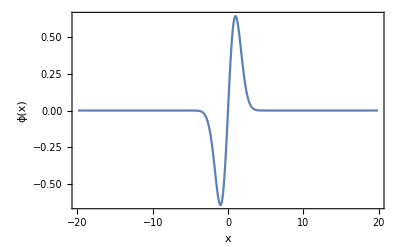

```mathematica
ListPlot[datawf,PlotRange->All,Frame->True,Joined->True,FrameLabel->{"x","ϕ(x)"},LabelStyle->Directive[Bold, Medium]]
```

#### Wigner function of the stationary state

```mathematica
wigner2=ListPlot3D[datawigner,PlotRange->{{-3,3},{-3,3},{-0.25,0.35}},AxesLabel->{"x","p","W"},LabelStyle->Directive[Bold,Medium]]
```

-Graphics3D-

```mathematica
wigner2=ListDensityPlot[datawigner,PlotRange->{{-3,3},{-3,3},All},Frame->True,FrameLabel->{"x","p"},LabelStyle->Directive[Bold,Medium],ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics-

#### Density of States (DOS) and Periods

```mathematica
dataenf=Flatten[dataen];
```

```mathematica
dos=Table[{(dataenf[[i+1]]+dataenf[[i]])/2,1/(dataenf[[i+1]]-dataenf[[i]])},{i,1,50}];
```

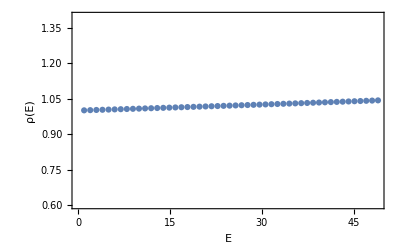

```mathematica
ListPlot[dos,PlotRange->{0.6,1.4},Frame->True, FrameLabel->{"E","ρ(E)"},LabelStyle->Directive[Bold, Medium]]
```